### Lista de Exercícios 1 - Arthur Silva Magalhães 12629595

#### 1)

```mathematica
x[t_] := A*Cos[ω*t +ϕ] (*Definindo a função de posição*)
v[t_] := -ω*A*Sin[ω*t +ϕ](*Definindo a função de velocidade*)
```

#### 2)

```mathematica
vw = Sqrt[2/1.75] (* valor ω com os valores de m e k fornecidos na questão *)
```

1.06904

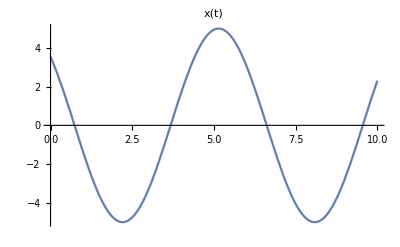

```mathematica
Plot[{x[t]/.{ω -> vw,A->5,ϕ->π/4}}, {t,0,10},PlotLabel->"x(t)"]
```

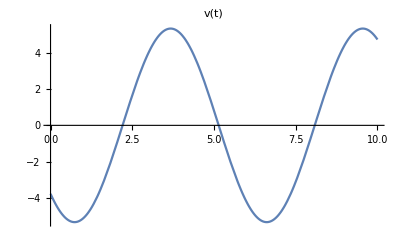

```mathematica
Plot[{v[t]/.{ω -> vw,A->5,ϕ->π/4}}, {t,0,10},PlotLabel->"v(t)"]
```

#### 3)

```mathematica
A = Sqrt[x0^2 + v0^2/ω^2] (*Definição de A*)
ϕ = ArcTan[- v0/(ω*x0)](*Definição de ϕ*)
```

√(x0^2+v0^2/ω^2)

-ArcTan[v0/(x0 ω)]

```mathematica
va = N[A/.{x0->0.25, v0 ->1.25,ω->vo}](*valor numérico de A*)
vp = N[ϕ/.{x0->0.25, v0 ->1.25,ω->vo}](*valor numérico de ϕ*)
```

1.1957

-1.36016

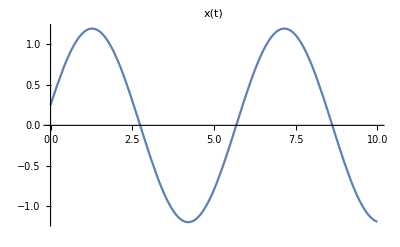

```mathematica
Plot[{x[t]/.{ω -> vw,A->va,ϕ->vp}}, {t,0,10},PlotLabel->"x(t)"]
```

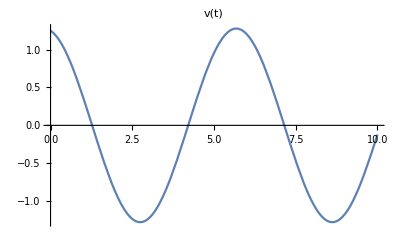

```mathematica
Plot[{v[t]/.{ω -> vw,A->va,ϕ->vp}}, {t,0,10},PlotLabel->"v(t)"]
```

#### 4)

```mathematica
K[t_] := 1/2*m*(-ω*va*Sin[ω*t +vp])^2(*Definindo a função de Energia Cinética*)
U[t_]:= 1/2*k*(va*Cos[ω*t +vp] )^2 (*Definindo a função de Energia Potencial*)
S[t_] := U[t]+K[t] (*Definindo a função da energia mecânica (Soma da Cinética e Potencial)*)
```

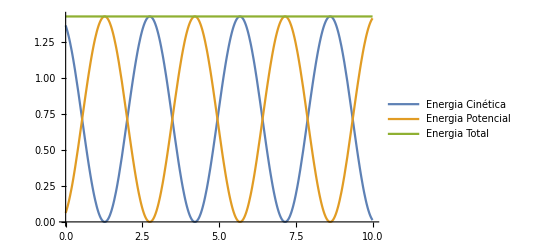

```mathematica
Plot[{K[t]/.{m->1.75,ω->vo} , U[t]/.{k-> 2,ω->vo}, S[t]/.{m->1.75,ω->vo,k->2}},{t,0,10},PlotLegends->{"Energia Cinética","Energia Potencial","Energia Total"}]
```